## Cellular Automata Solution

Hello and welcome to our solution to the Cellular Automaton project. Let’s get started.

The first thing to do is to create the rules, which depend on the current state of a cell and its two neighbors. So in order to do that, we first enumerate all the possible neighborhoods. Consider a cell and its two neighbors. Each triplet defines a possible neighborhood for a given state. The next step is determined based on the state of this neighborhood. There are 2^3=8 neighborhoods for a two-colored nearest neighbor Cellular Automaton.

```mathematica
Tuples[{1,0},3]
```

{{1,1,1},{1,1,0},{1,0,1},{1,0,0},{0,1,1},{0,1,0},{0,0,1},{0,0,0}}

As we said before, the update rule for the Cellular Automaton is determined by the binary representation of the rule number (between 0 and 255).  We can get the binary representation of a number using IntegerDigits:

```mathematica
?IntegerDigits
```

RowBox[{"IntegerDigits", "[", StyleBox["n", "TI"], "]"}] gives a list of the decimal digits in the integer StyleBox["n", "TI"]. 
RowBox[{"IntegerDigits", "[", RowBox[{StyleBox["n", "TI"], ",", StyleBox["b", "TI"]}], "]"}] gives a list of the base StyleBox["b", "TI"] digits in the integer StyleBox["n", "TI"]. 
RowBox[{"IntegerDigits", "[", RowBox[{StyleBox["n", "TI"], ",", StyleBox["b", "TI"], ",", StyleBox["len", "TI"]}], "]"}] pads the list on the left with zeros to give a list of length StyleBox["len", "TI"]. 
RowBox[{"IntegerDigits", "[", RowBox[{StyleBox["n", "TI"], ",", RowBox[{"MixedRadix", "[", StyleBox["blist", "TI"], "]"}]}], "]"}] uses the mixed radix with list of bases StyleBox["blist", "TI"].

Since we have 8 possible neighborhoods, we pad our binary list to length 8 using the third form:

```mathematica
IntegerDigits[90,2,8]
```

{0,1,0,1,1,0,1,0}

Now we create a list of rules, by threading Rule over Tuples and IntegerDigits:

```mathematica
?Thread
```

RowBox[{"Thread", "[", RowBox[{StyleBox["f", "TI"], "[", StyleBox["args", "TI"], "]"}], "]"}] "threads" StyleBox["f", "TI"] over any lists that appear in StyleBox["args", "TI"]. 
RowBox[{"Thread", "[", RowBox[{RowBox[{StyleBox["f", "TI"], "[", StyleBox["args", "TI"], "]"}], ",", StyleBox["h", "TI"]}], "]"}] threads StyleBox["f", "TI"] over any objects with head StyleBox["h", "TI"] that appear in StyleBox["args", "TI"]. 
RowBox[{"Thread", "[", RowBox[{RowBox[{StyleBox["f", "TI"], "[", StyleBox["args", "TI"], "]"}], ",", StyleBox["h", "TI"], ",", StyleBox["n", "TI"]}], "]"}] threads StyleBox["f", "TI"] over objects with head StyleBox["h", "TI"] that appear in the first StyleBox["n", "TI"] StyleBox["args", "TI"].

```mathematica
Thread[Rule[Tuples[{1,0},3],IntegerDigits[90,2,8]]]
```

{{1,1,1}→0,{1,1,0}→1,{1,0,1}→0,{1,0,0}→1,{0,1,1}→1,{0,1,0}→0,{0,0,1}→1,{0,0,0}→0}

So this says the neighborhood {1,1,1} goes to 0 in the next state, as well as the next two. Then, {1,0,0} goes to 1 , and so on.

So now we have our rules defined. We need to apply this to a given row of example cells state.

```mathematica
state = {1,0,1,0,0}
```

{1,0,1,0,0}

In order for rule list be able to match the entries in the state array, we need to partition state array into overlapping groups of three.

```mathematica
?Partition
```

RowBox[{"Partition", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"]}], "]"}] partitions StyleBox["list", "TI"] into nonoverlapping sublists of length StyleBox["n", "TI"]. 
RowBox[{"Partition", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"], ",", StyleBox["d", "TI"]}], "]"}] generates sublists with offset StyleBox["d", "TI"]. 
RowBox[{"Partition", "[", RowBox[{StyleBox["list", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] partitions a nested list into blocks of size SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]]×SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]]×….
RowBox[{"Partition", "[", RowBox[{StyleBox["list", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["d", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["d", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] uses offset SubscriptBox[StyleBox["d", "TI"], StyleBox["i", "TI"]] at level StyleBox["i", "TI"] in StyleBox["list", "TI"]. 
RowBox[{"Partition", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"], ",", StyleBox["d", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["k", "TI"], StyleBox["L", "TI"]], ",", SubscriptBox[StyleBox["k", "TI"], StyleBox["R", "TI"]]}], "}"}]}], "]"}] specifies that the first element of StyleBox["list", "TI"] should appear at position SubscriptBox[StyleBox["k", "TI"], StyleBox["L", "TI"]] in the first sublist, and the last element of StyleBox["list", "TI"] should appear at or after position SubscriptBox[StyleBox["k", "TI"], StyleBox["R", "TI"]] in the last sublist. If additional elements are needed, Partition fills them in by treating StyleBox["list", "TI"] as cyclic. 
RowBox[{"Partition", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"], ",", StyleBox["d", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["k", "TI"], StyleBox["L", "TI"]], ",", SubscriptBox[StyleBox["k", "TI"], StyleBox["R", "TI"]]}], "}"}], ",", StyleBox["x", "TI"]}], "]"}] pads if necessary by repeating the element StyleBox["x", "TI"]. 
RowBox[{"Partition", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"], ",", StyleBox["d", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["k", "TI"], StyleBox["L", "TI"]], ",", SubscriptBox[StyleBox["k", "TI"], StyleBox["R", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] pads if necessary by cyclically repeating the elements SubscriptBox[StyleBox["x", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"Partition", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"], ",", StyleBox["d", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["k", "TI"], StyleBox["L", "TI"]], ",", SubscriptBox[StyleBox["k", "TI"], StyleBox["R", "TI"]]}], "}"}], ",", RowBox[{"{", "}"}]}], "]"}] uses no padding, and so can yield sublists of different lengths. 
RowBox[{"Partition", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["nlist", "TI"], ",", StyleBox["dlist", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["klist", "TI"], StyleBox["L", "TI"]], ",", SubscriptBox[StyleBox["klist", "TI"], StyleBox["R", "TI"]]}], "}"}], ",", StyleBox["padlist", "TI"]}], "]"}] specifies alignments and padding in a nested list.

```mathematica
Partition[state, 3]
```

{{1,0,1}}

Not quite right. In order to get it to overlap, partitioning needs to be done with an offset of 1 using the second form.

```mathematica
Partition[state, 3,1]
```

{{1,0,1},{0,1,0},{1,0,0}}

Almost there. The next state must have five cells, but we only have three. The problem is in the boundary conditions. They need to be defined cyclically, i.e. the left most cell must consider the right most cell as its left neighbor, and vice versa. We can accomplish that by doing:

```mathematica
Partition[state, 3,1,2]
```

{{0,1,0},{1,0,1},{0,1,0},{1,0,0},{0,0,1}}

Awesome!

Now let’s apply our rule.

```mathematica
Partition[state, 3,1,2]/.Thread[Rule[Tuples[{1,0},3],IntegerDigits[90,2,8]]]
```

{0,0,0,1,1}

Great.

We can visualize this evolution step with ArrayPlot.

```mathematica
?ArrayPlot
```

RowBox[{"ArrayPlot", "[", StyleBox["array", "TI"], "]"}] generates a plot in which the values in an array are shown in a discrete array of squares.

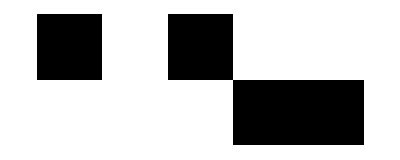

```mathematica
ArrayPlot[{state,Partition[state, 3,1,2]/.Thread[Rule[Tuples[{1,0},3],IntegerDigits[90,2,8]]]},ImageSize->Full]
```

Now let’s make a function out of all of this, which takes care of one step of the evolution.

```mathematica
CAStep[rule_Integer,init_List]:=Partition[init, 3,1,2]/.Thread[Rule[Tuples[{1,0},3],IntegerDigits[rule,2,8]]]
```

```mathematica
CAStep[90,{0,0,1,0,0}]
```

{0,1,0,1,0}

Now we just need to keep applying the same rule on the new state. Let’s use NestList.

```mathematica
NestList[CAStep[90, #]&,{0,0,1,0,0},3]
```

{{0,0,1,0,0},{0,1,0,1,0},{1,0,0,0,1},{1,1,0,1,1}}

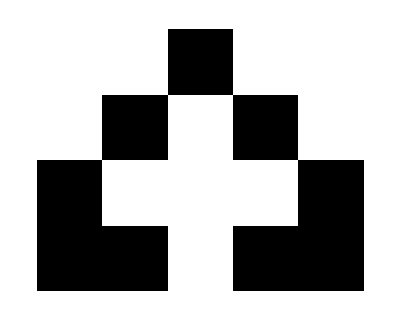

```mathematica
NestList[CAStep[90, #]&,{0,0,1,0,0},3]//ArrayPlot
```

We’ll write this as a function.

```mathematica
CAEvolve[rule_Integer/;rule<256,init_List,t_Integer/;t>0]:=NestList[CAStep[rule, #]&,init,t]
```

We can ArrayPlot it.

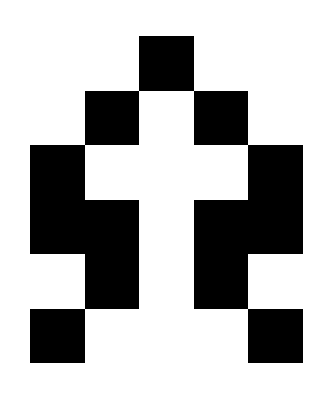

```mathematica
ArrayPlot[CAEvolve[90,{0,0,1,0,0},5]]
```

As you can see the width of the simulation remains constant. We want this to grow as we increase the number of steps. So we set the width of our initial condition to depend on number of time steps.

```mathematica
?ArrayPad
```

RowBox[{"ArrayPad", "[", RowBox[{StyleBox["array", "TI"], ",", StyleBox["m", "TI"]}], "]"}] gives an array with StyleBox["m", "TI"] 0s of padding on every side. 
RowBox[{"ArrayPad", "[", RowBox[{StyleBox["array", "TI"], ",", StyleBox["m", "TI"], ",", StyleBox["padding", "TI"]}], "]"}] uses the specified padding.
RowBox[{"ArrayPad", "[", RowBox[{StyleBox["array", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["m", "TI"], ",", StyleBox["n", "TI"]}], "}"}], ",", StyleBox["…", "TR"]}], "]"}] pads with StyleBox["m", "TI"] elements at the beginning and StyleBox["n", "TI"] elements at the end. 
RowBox[{"ArrayPad", "[", RowBox[{StyleBox["array", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["m", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["m", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "]"}] pads with SubscriptBox[StyleBox["m", "TI"], StyleBox["i", "TI"]], SubscriptBox[StyleBox["n", "TI"], StyleBox["i", "TI"]] elements at level StyleBox["i", "TI"] in StyleBox["array", "TI"].

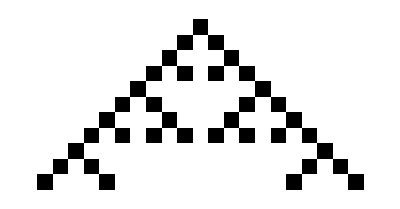

```mathematica
ArrayPlot[CAEvolve[90,ArrayPad[{1},10],10]]
```

Let’s browse through the rule space, by putting this in Manipulate.

```mathematica
Manipulate[ArrayPlot[
CAEvolve[r,ArrayPad[{1},t],t]],
{{r,90,"Rule Number"},0,255,1},
{{t,30,"Time Step"},1,100,1}]
```